```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gabrielsalcedo/Documentos/UNISON-UADY-Project/programas

```mathematica
FNames=FileNames["*Clases.csv"];
Fk[k_]:=Import[FNames[[k]]]
```

```mathematica
FNames
FNames[[1]]
```

{ControlClases.csv,NoControlClases.csv}

ControlClases.csv

```mathematica
AmatC = Fk[1];
AmatNC = Fk[2];
```

```mathematica
Dimensions[AmatC]
Dimensions[AmatNC]
```

{362,10}

{362,10}

```mathematica
tvecC = AmatC[[All,1]];
tvecNC = AmatNC[[All,1]];
```

```mathematica
xclases={"L","S","E","I_S","I_A","H","R","D","V"};
dim=Length[xclases]
```

9

```mathematica
Optimal and no optimal controlled dynamics
```

and controlled dynamics no optimal Optimal

```mathematica
and controlled dynamics no optimal Optimal
```

and controlled dynamics no optimal Optimal

```mathematica
plotdatC[k_]:= 
ListPlot[
Thread[{tvecC,AmatC[[All,k+1]]}],
PlotStyle->{Thick,Blue},
AxesLabel->{"t",xclases[[k]]}
]
plotdatNC[k_]:=
ListPlot[
Thread[{tvecNC,AmatNC[[All,k+1]]}],
PlotStyle->{Thick,Red},AxesLabel->{"t",xclases[[k]]},PlotRange->All]
```

```mathematica
PltTime=tvecC;
Lck = AmatC[[All,2]];
S = AmatC[[All,3]];
Ex = AmatC[[All,4]];
IS =AmatC[[All,5]];
IA = AmatC[[All,6]];
H= AmatC[[All,7]] ;
R = AmatC[[All,8]];
Dcov = AmatC[[All,9]];
Vac = AmatC[[All,10]];
```

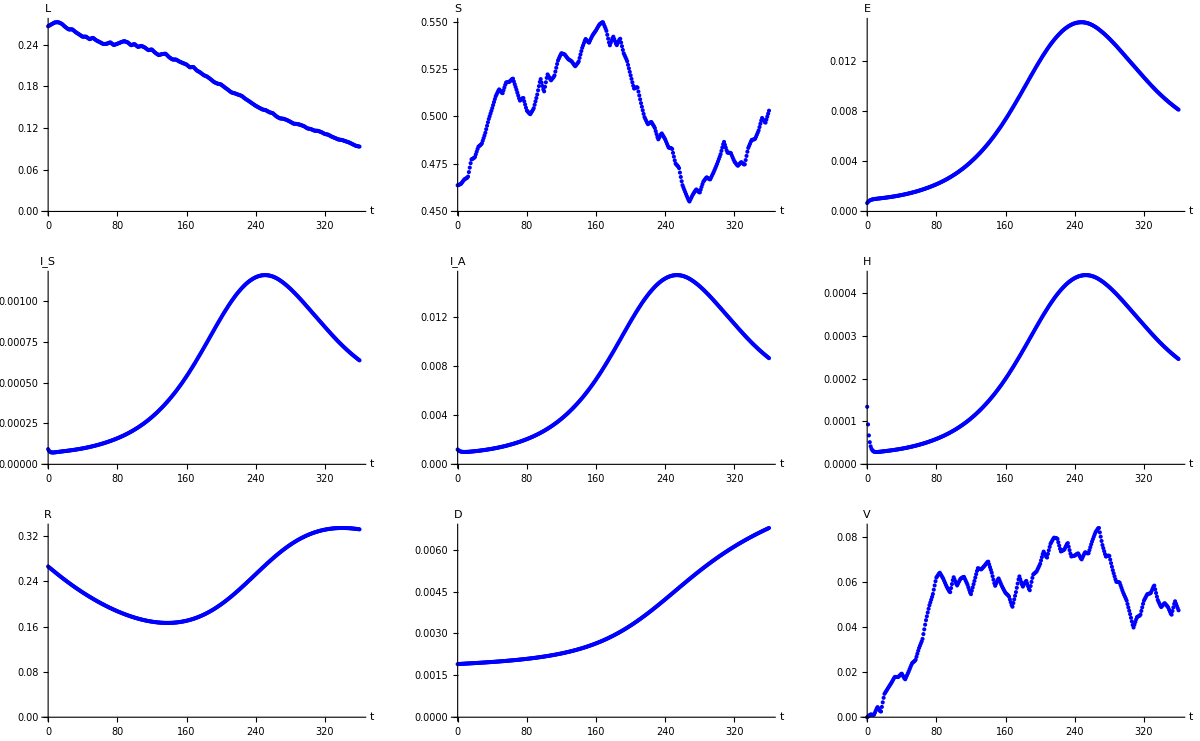

```mathematica
(*Clases controladas*)
GraphicsGrid[
{
{plotdatC[1],plotdatC[2], plotdatC[3]},
{plotdatC[4],plotdatC[5], plotdatC[6]},
{plotdatC[7],plotdatC[8], plotdatC[9]}
}
]
```

```mathematica
Her we need to run the dynamics without vaccination
```

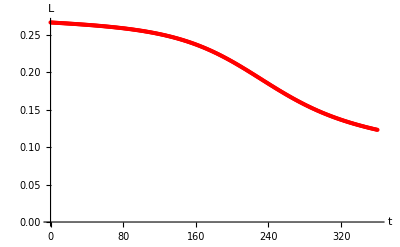
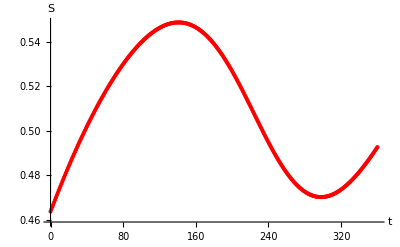
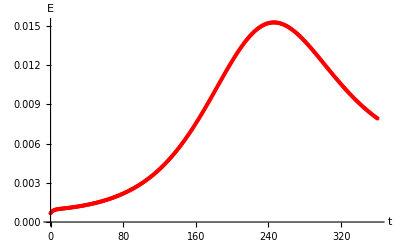
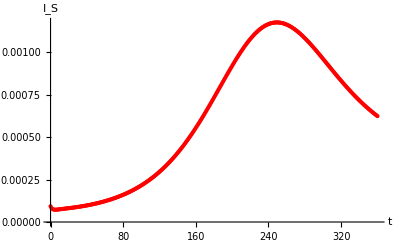
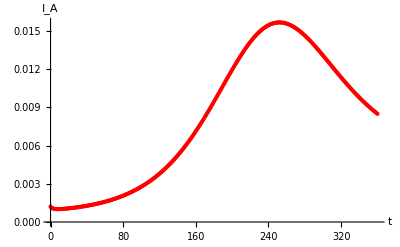
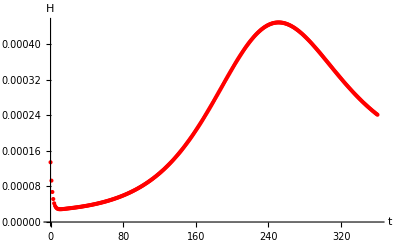
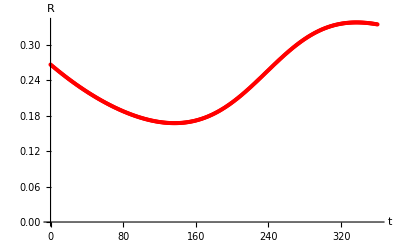
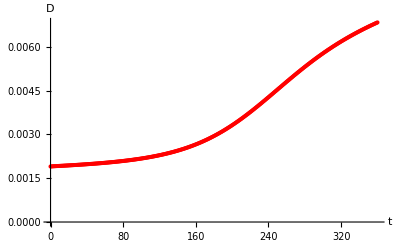

```mathematica
(*Clases NO optimized*)
Table[plotdatNC[k],{k,1,dim}]
```

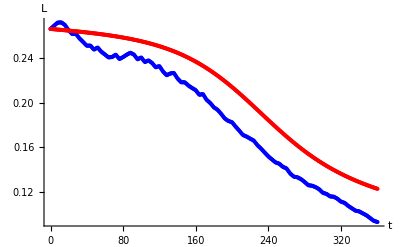
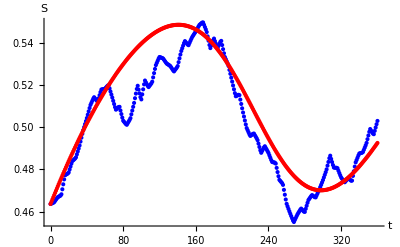
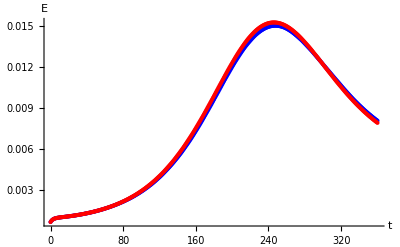
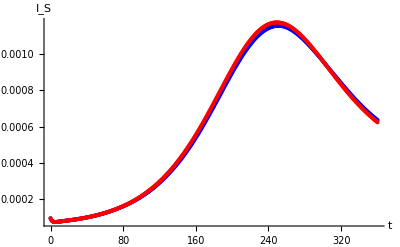
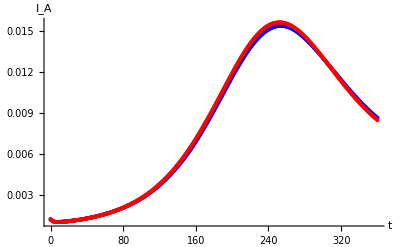
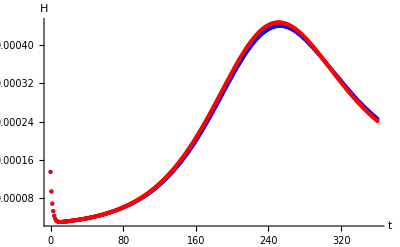
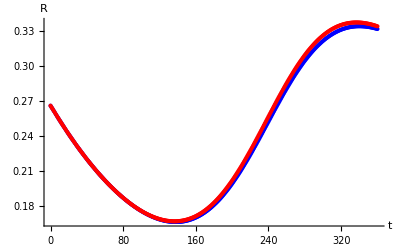
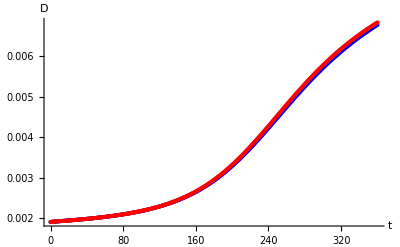

```mathematica
Table[Show[plotdatC[k],plotdatNC[k], PlotRange->All],{k,1,dim}]
```